```mathematica
F[xmm_,rhogpercc_,mu_,sigma_]:=6/(Pi*rhogpercc*10^-6*sigma*Sqrt[2*Pi])*(1-Erf[(Log[xmm]-mu+3*sigma^2)/(Sqrt[2]*sigma)])*Exp[-3*mu+9/2*sigma^2]
F1[xmm_,rhogpercc_,mu_,sigma_]:=
Fapprox[xmm_,rhogpercc_]:=2.7695*10^4*3.1/rhogpercc/((xmm/0.7126)^4.3026+(xmm)^2.8849)
Xm[massg_,rhogpercc_]:=(6*massg/(Pi*rhogpercc))^(1/3)*10
```

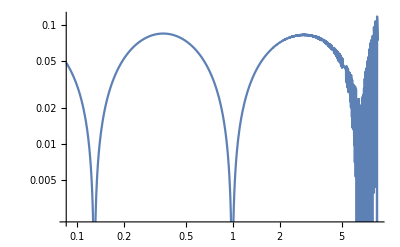

```mathematica
LogLogPlot[{Abs[(F[x,3.1,-2.649,1.786]-Fapprox[x,3.1])]/F[x,3.1,-2.649,1.786]},{x,Xm[10^-6,3.1],Xm[1,3.1]}]
```

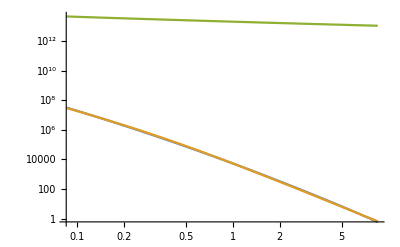

```mathematica
LogLogPlot[{F[x,3.1,-2.649,1.786],Fapprox[x,3.1],F1[x,3.1,-2.649,1.786]},{x,Xm[10^-6,3.1],Xm[1,3.1]}]
```

```mathematica
MaxValue[{Abs[(F[x,3.1,-2.649,1.786]-Fapprox[x,3.1])]/F[x,3.1,-2.649,1.786],{x>=Xm[10^-6,3.1], x<=Xm[1,3.1]}},x]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

0.125416

```mathematica
F[Xm[10^-6,3.1],3.1,-2.649,1.786]
```

3.14644×10^7

```mathematica
Xm[10^-6,3.1]
```

0.0850903